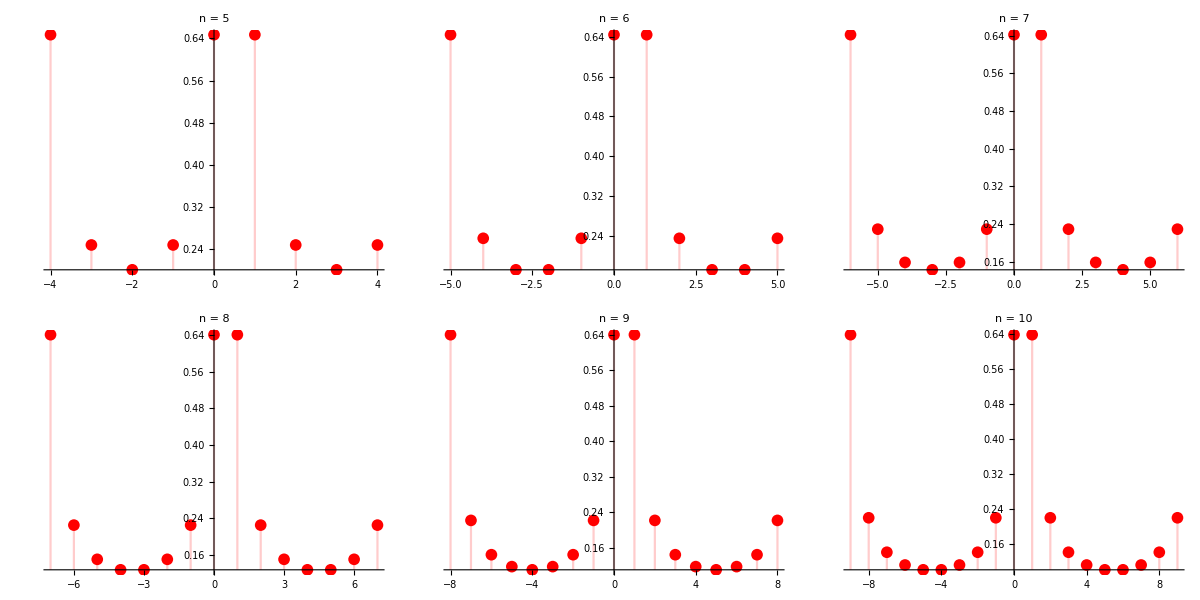

```mathematica
F[k_,n_,x_]:=Abs[Sinc[π (k-x)]/Sinc[π (k-x)/n]];
Grid[ArrayReshape[Table[DiscretePlot[F[k,n,0.5],{k,-(n- 1),n - 1},PlotLabel->StringForm["n = `1`",n],PlotStyle->Red,PlotMarkers->Style["•", FontSize -> 12],PlotRange->Full],{n,5, 10,1}],{2,3}]]
```

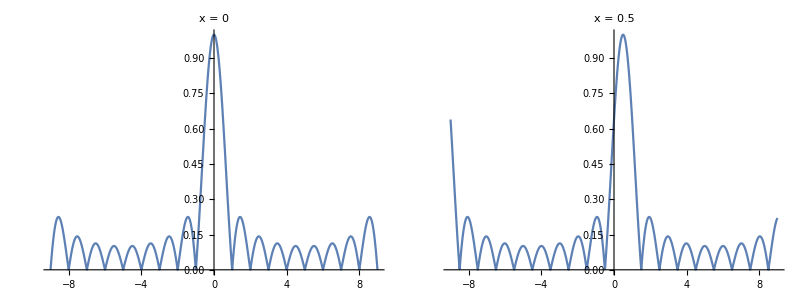

```mathematica
Grid[{Table[Plot[F[x,10,t],{x,-9,9},PlotRange->Full,PlotLabel->StringForm["x = `1`",t]],{t ,{0,0.5}}]}]
```